```mathematica
Clear["Global`*"]
```

#### Shape function definitions

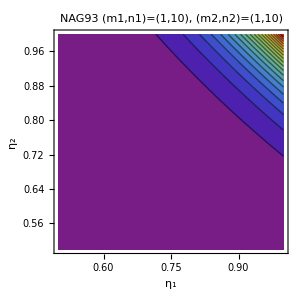

```mathematica
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]

(*1D AG-3 shape functions*)
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])

NAG91[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[η1,m1,n1]*NAG3one[η2,m2,n2]
NAG92[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[η1,m1,n1]*NAG3one[η2,m2,n2]
NAG93[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[η1,m1,n1]*NAG3three[η2,m2,n2]
NAG94[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[η1,m1,n1]*NAG3three[η2,m2,n2]
NAG95[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[η1,m1,n1]*NAG3one[η2,m2,n2]
NAG96[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[η1,m1,n1]*NAG3two[η2,m2,n2]
NAG97[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[η1,m1,n1]*NAG3three[η2,m2,n2]
NAG98[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[η1,m1,n1]*NAG3two[η2,m2,n2]
NAG99[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[η1,m1,n1]*NAG3two[η2,m2,n2]

m1=1;n1=10;
m2=1;n2=10;

Nshape={
NAG91[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG92[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG93[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG94[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG95[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG96[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG97[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG98[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG99[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

funcs={NAG91,NAG92,NAG93,NAG94,NAG95,NAG96,NAG97,NAG98,NAG99};
labels={"NAG91","NAG92","NAG93","NAG94","NAG95","NAG96","NAG97","NAG98","NAG99"};

Table[ContourPlot[funcs[[i]][η1,η2,m1,n1,m2,n2],{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
PlotLabel->Style[labels[[i]]<>"\n (m1,n1)=("<>ToString[m1]<>","<>ToString[n1]<>"), (m2,n2)=("<>ToString[m2]<>","<>ToString[n2]<>")",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300],{i,1,9}];

Table[Plot3D[funcs[[i]][η1,η2,m1,n1,m2,n2],{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
PlotLabel->Style[labels[[i]]<>"\n (m1,n1)=("<>ToString[m1]<>","<>ToString[n1]<>"), (m2,n2)=("<>ToString[m2]<>","<>ToString[n2]<>")",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300],{i,1,9}];

ContourPlot[funcs[[3]][η1,η2,m1,n1,m2,n2],{η1,0.5,1},{η2,0.5,1},PlotRange->All,PlotPoints->50,MaxRecursion->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",ColorFunctionScaling->True,FrameLabel->{Style["η₁",14],Style["η₂",14]},PlotLabel->Style[labels[[3]]<>"\n (m1,n1)=("<>ToString[m1]<>","<>ToString[n1]<>"), (m2,n2)=("<>ToString[m2]<>","<>ToString[n2]<>")",14],ImageSize->300]
```

#### Test 0 (Edge offset, Center offset)=(0.,0.)

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0},{0,0}}

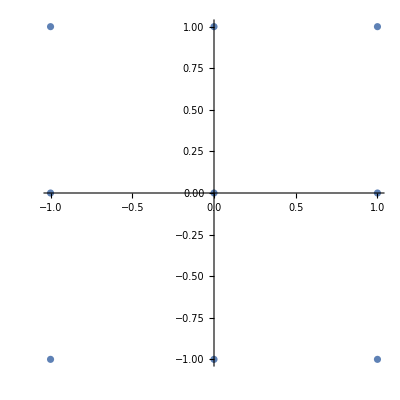

n8(0.3,0.3)={0,0}

n6(0.3,0.3)={1,0}

```mathematica
m1=1;n1=1;
m2=1;n2=1;
β=0;

Nshape={
NAG91[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG92[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG93[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG94[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG95[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG96[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG97[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG98[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG99[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

coord={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,β},{β,1},{-1,0},{β,β}}
ListPlot[coord,AspectRatio->1]

{x,y}=Nshape.coord;

mapped={x,y}/.{η1->0,η2->0};
Print["n8(0.3,0.3)=",mapped]

mapped={x,y}/.{η1->1,η2->0};
Print["n6(0.3,0.3)=",mapped]

Plot3D[x,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
Plot3D[y,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

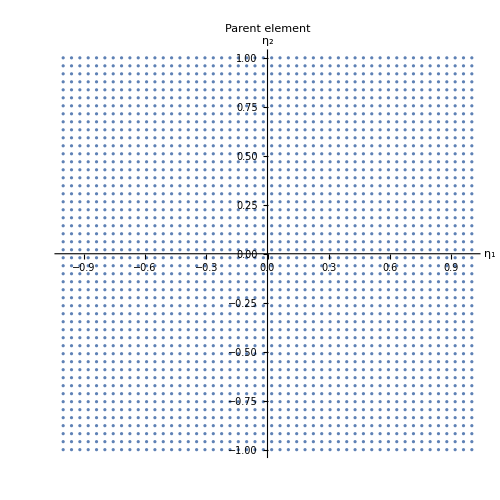
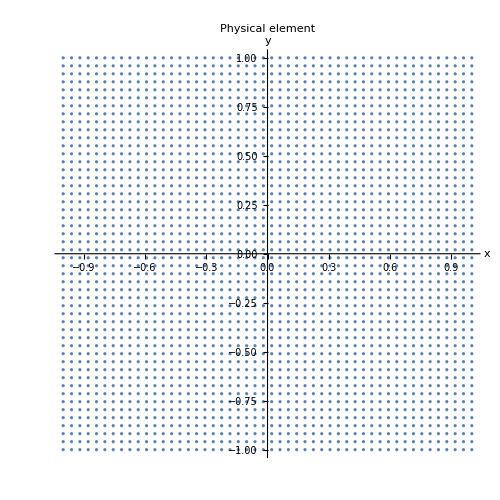

```mathematica
n=50;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}]
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];
```

-Graphics3D-

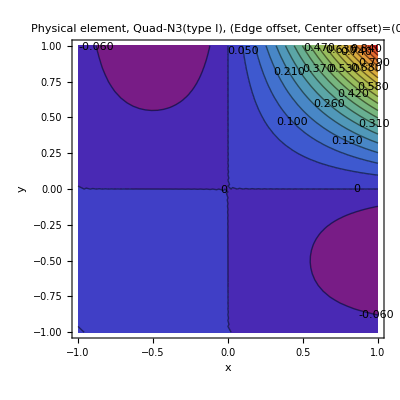

```mathematica
{m1,n1}={1,1};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

{xmin,xmax}=MinMax[N3data3D[[All,1]]];
{ymin,ymax}=MinMax[N3data3D[[All,2]]];
plane=Graphics3D[{Yellow,Opacity[0.7],Polygon[{{xmin,ymin,0},{xmax,ymin,0},{xmax,ymax,0},{xmin,ymax,0}}]}];

Show[ListPointPlot3D[N3data3D,PlotStyle->Black,PlotRange->All,PlotLabel->Style["Physical element, Quad-N3(type I),\n  (Edge offset, Center offset)=(0.,0.)",Bold,14],ImageSize->250]
,plane]

ListContourPlot[N3data3D,PlotLabel->Style["Physical element, Quad-N3(type I),  \n(Edge offset, Center offset)=(0.,0.)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}],PlotRange->All]
```

-Graphics3D-

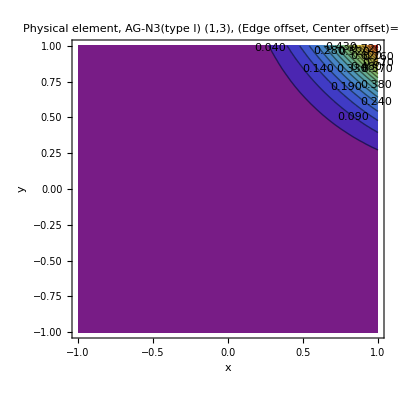

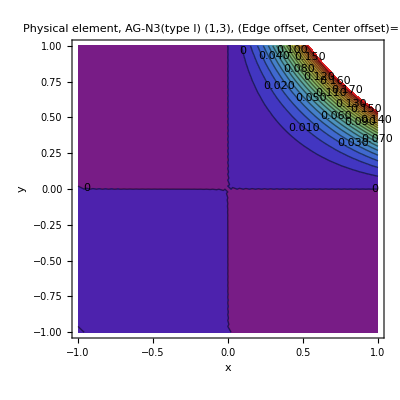

```mathematica
{m1,n1}={1,3};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->All,PlotStyle->Black,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,0.)",Bold,14]],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,0.)",Bold, 14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}]]

ListContourPlot[N3data3D,PlotRange->{All,0.19},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,0.)",Bold, 14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}]]
```

#### Test 1 (Edge offset, Center offset)=(0.2,0.2)

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0.2},{0.2,1},{-1,0},{0.2,0.2}}

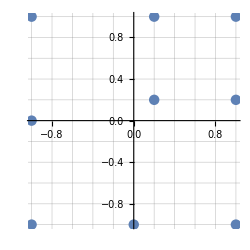

n8(0.3,0.3)={0.2,0.2}

n6(0.3,0.3)={1.,0.2}

```mathematica
m1=1;n1=1;
m2=1;n2=1;
β=0.2;

Nshape={
NAG91[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG92[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG93[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG94[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG95[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG96[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG97[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG98[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG99[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

coord={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,β},{β,1},{-1,0},{β,β}}

ListPlot[coord, AspectRatio->1,ImageSize->250, PlotStyle->PointSize[0.03],GridLines->{Subdivide[-1.,1.,10], Subdivide[-1.,1.,10]}]

{x,y}=Nshape.coord;

mapped={x,y}/.{η1->0,η2->0};
Print["n8(0.3,0.3)=",mapped]

mapped={x,y}/.{η1->1,η2->0};
Print["n6(0.3,0.3)=",mapped]

Plot3D[x,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
Plot3D[y,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
```

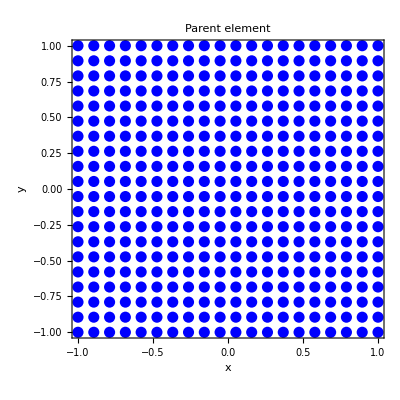

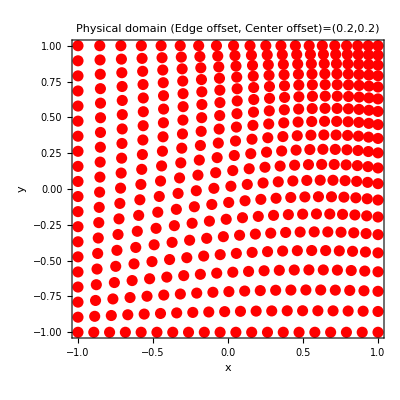

```mathematica
n=20;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}];
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",Bold,16],Frame->True,PlotStyle->{Blue,PointSize[0.02]},
AxesLabel->{Style["x",Bold,16],Style["y",Bold,16],None},ColorFunctionScaling->True,Mesh->True,ImageSize->400,AspectRatio->1]
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical domain (Edge offset, Center offset)=(0.2,0.2)",Bold,16],Frame->True,PlotStyle->{Red,PointSize[0.02]},
AxesLabel->{Style["x",Bold,16],Style["y",Bold,16],None},ColorFunctionScaling->True,Mesh->True,ImageSize->400,AspectRatio->1]
```

```mathematica
n=50;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}];
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];
```

-Graphics3D-

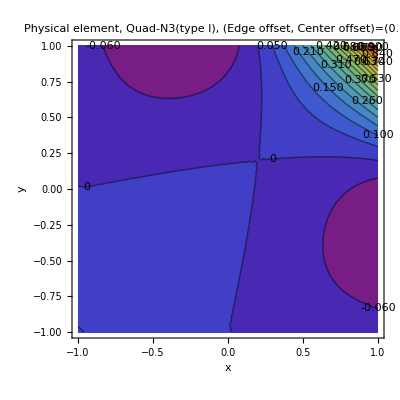

```mathematica
{m1,n1}={1,1};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, Quad-N3(type I),\n  (Edge offset, Center offset)=(0.2,0.2)",Bold,14],PlotStyle->Black],plane]

ListContourPlot[N3data3D,PlotLabel->Style["Physical element, Quad-N3(type I),  \n(Edge offset, Center offset)=(0.2,0.2)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}],PlotRange->All]
```

-Graphics3D-

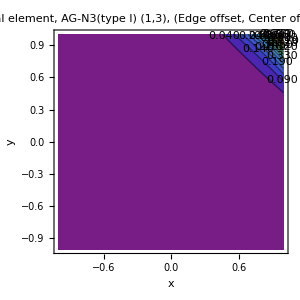

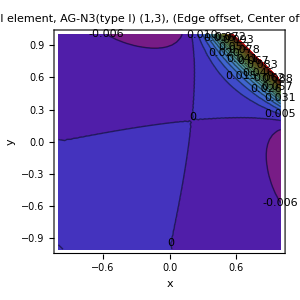

```mathematica
{m1,n1}={1,3};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.2,0.2)",Bold,14],PlotStyle->Black],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.2,0.2)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]

ListContourPlot[N3data3D,PlotRange->{All,0.1},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.2,0.2)",Bold, 14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]
```

#### Test 2: (shift center node)(Edge offset, Center offset)=(0.2,0.1)

0.1

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0.2},{0.2,1},{-1,0},{0.1,0.1}}

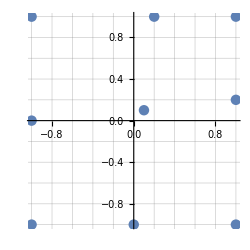

n8(0.3,0.3)={0.1,0.1}

n6(0.3,0.3)={1.,0.2}

```mathematica
m1=1;n1=1;
m2=1;n2=1;
β=0.2;
β1=0.1

Nshape={
NAG91[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG92[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG93[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG94[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG95[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG96[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG97[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG98[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG99[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

coord={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,β},{β,1},{-1,0},{β1,β1}}
ListPlot[coord, AspectRatio->1,ImageSize->250, PlotStyle->PointSize[0.03],GridLines->{Subdivide[-1.,1.,10], Subdivide[-1.,1.,10]}]
{x,y}=Nshape.coord;

mapped={x,y}/.{η1->0,η2->0};
Print["n8(0.3,0.3)=",mapped]

mapped={x,y}/.{η1->1,η2->0};
Print["n6(0.3,0.3)=",mapped]

Plot3D[x,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
Plot3D[y,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
```

-Graphics-

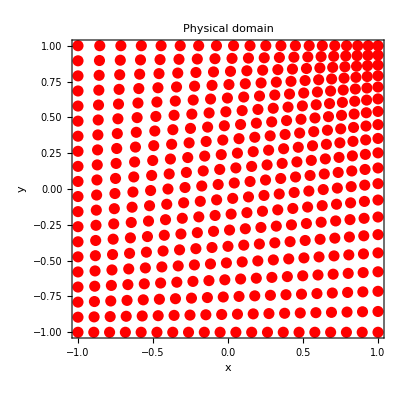

```mathematica
n=20;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}];
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",Bold,16],Frame->True,PlotStyle->{Blue,PointSize[0.02]},
AxesLabel->{Style["x",Bold,16],Style["y",Bold,16],None},ColorFunctionScaling->True,Mesh->True,ImageSize->400,AspectRatio->1]
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical domain",Bold,16],Frame->True,PlotStyle->{Red,PointSize[0.02]},
AxesLabel->{Style["x",Bold,16],Style["y",Bold,16],None},ColorFunctionScaling->True,Mesh->True,ImageSize->400,AspectRatio->1]
```

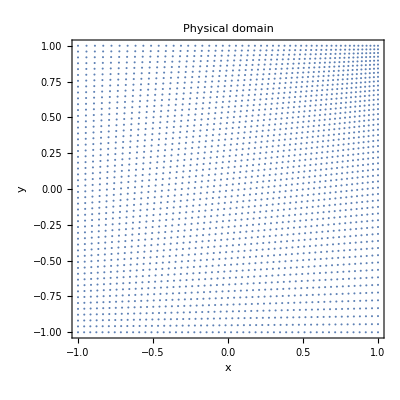

```mathematica
n=50;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}];
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical domain",Bold,16],Frame->True,
AxesLabel->{Style["x",Bold,16],Style["y",Bold,16],None},ColorFunctionScaling->True,Mesh->True,ImageSize->400,AspectRatio->1]

Table[{parentplot,physicalplot}];
```

```mathematica
{m1,n1}={1,1};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.2,0.1)",14],PlotStyle->Black],plane]

ListContourPlot[N3data3D,PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.2,0.1)",14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}],PlotRange->All]
```

Show::gcomb: Could not combine the graphics objects in Show[,plane].

Show[-Graphics3D-,plane]

-Graphics-

```mathematica
ListContourPlot[N3data3D,PlotRange->{{0.5,1},{0.5,1},All},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.2,0.1)",14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}]]
```

-Graphics-

```mathematica
{m1,n1}={1,3};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.2,0.1)",14],PlotStyle->Black],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.2,0.1)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}],FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]

ListContourPlot[N3data3D,PlotRange->{All,0.1},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.2,0.1)",Bold, 14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]
```

Show::gcomb: Could not combine the graphics objects in Show[,plane].

Show[-Graphics3D-,plane]

-Graphics-

-Graphics-

#### Test 3: (shift center node)(Edge offset, Center offset)=(0.,-0.1)

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0},{-0.1,-0.1}}

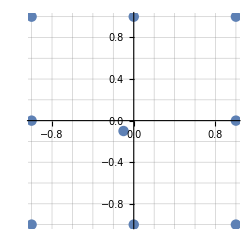

n8(0.3,0.3)={-0.1,-0.1}

n6(0.3,0.3)={1.,0.}

```mathematica
m1=1;n1=1;
m2=1;n2=1;
β=0;
β1=-0.1;

Nshape={
NAG91[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG92[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG93[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG94[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG95[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG96[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG97[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG98[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG99[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

coord={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,β},{β,1},{-1,0},{β1,β1}}
ListPlot[coord, AspectRatio->1,ImageSize->250, PlotStyle->PointSize[0.03],GridLines->{Subdivide[-1.,1.,10], Subdivide[-1.,1.,10]}]
{x,y}=Nshape.coord;

mapped={x,y}/.{η1->0,η2->0};
Print["n8(0.3,0.3)=",mapped]

mapped={x,y}/.{η1->1,η2->0};
Print["n6(0.3,0.3)=",mapped]

Plot3D[x,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
Plot3D[y,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
```

-Graphics3D-

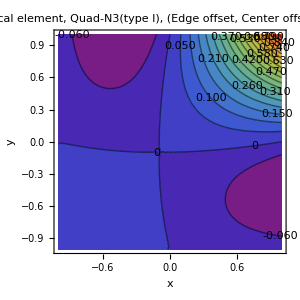

```mathematica
n=50;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}];
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

{m1,n1}={1,1};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],PlotStyle->Black,ImageSize->300],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},PlotLegends->BarLegend[{"Rainbow",Automatic}],ImageSize->300]
```

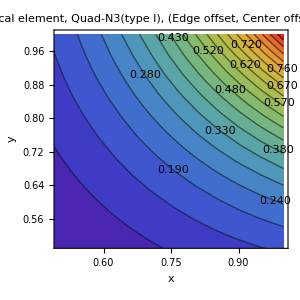

```mathematica
ListContourPlot[N3data3D,PlotRange->{{0.5,1},{0.5,1},All},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},PlotLegends->BarLegend[{"Rainbow",Automatic}],ImageSize->300]
```

-Graphics3D-

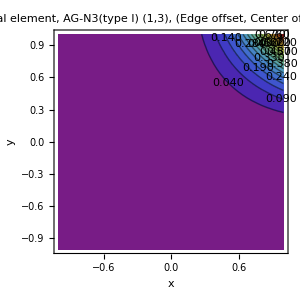

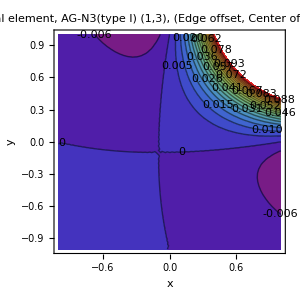

```mathematica
{m1,n1}={1,3};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],PlotStyle->Black,ImageSize->300],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}],FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]

ListContourPlot[N3data3D,PlotRange->{All,0.1},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.1)",Bold, 14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]
```

#### Test 3: (shift center node)(Edge offset, Center offset)=(0.,-0.2)

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0},{-0.2,-0.2}}

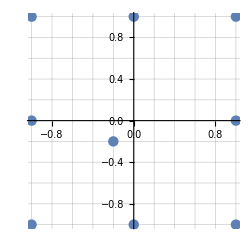

n8(0.3,0.3)={-0.2,-0.2}

n6(0.3,0.3)={1.,0.}

```mathematica
m1=1;n1=1;
m2=1;n2=1;
β=0;
β1=-0.2;

Nshape={
NAG91[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG92[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG93[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG94[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG95[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG96[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG97[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG98[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG99[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

coord={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,β},{β,1},{-1,0},{β1,β1}}
ListPlot[coord, AspectRatio->1,ImageSize->250, PlotStyle->PointSize[0.03],GridLines->{Subdivide[-1.,1.,10], Subdivide[-1.,1.,10]}]
{x,y}=Nshape.coord;

mapped={x,y}/.{η1->0,η2->0};
Print["n8(0.3,0.3)=",mapped]

mapped={x,y}/.{η1->1,η2->0};
Print["n6(0.3,0.3)=",mapped]

Plot3D[x,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
Plot3D[y,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
```

-Graphics3D-

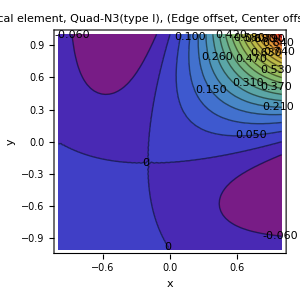

```mathematica
n=50;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}];
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

{m1,n1}={1,1};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.2)",Bold,14],PlotStyle->Black,ImageSize->300],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.2)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},PlotLegends->BarLegend[{"Rainbow",Automatic}],ImageSize->300]
```

```mathematica
ListContourPlot[N3data3D,PlotRange->{{0.5,1},{0.5,1},All},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.2)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},PlotLegends->BarLegend[{"Rainbow",Automatic}],ImageSize->300]
```

-Graphics-

-Graphics3D-

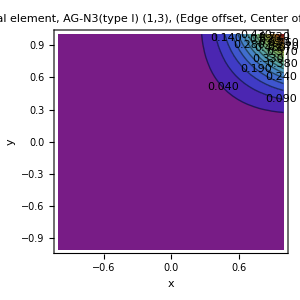

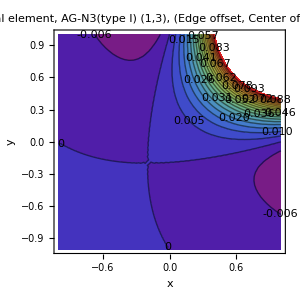

```mathematica
{m1,n1}={1,3};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.2)",Bold,14],PlotStyle->Black,ImageSize->300],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.2)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}],FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]

ListContourPlot[N3data3D,PlotRange->{All,0.1},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.2)",Bold, 14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]
```

#### Comparison

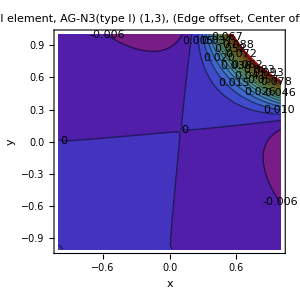

#### Integral Test 1: shift center node, (Center offset) (dx,dy)=(-0.1,-0.1)

```mathematica
m1=1;n1=1;
m2=1;n2=1;
β=0;
β1=-0.1;

Nshape={
NAG91[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG92[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG93[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG94[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG95[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG96[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG97[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG98[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG99[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

coord={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,β},{β,1},{-1,0},{β1,β1}}
ListPlot[coord, AspectRatio->1,ImageSize->250, PlotStyle->PointSize[0.03],GridLines->{Subdivide[-1.,1.,10], Subdivide[-1.,1.,10]}]
{x,y}=Nshape.coord;

mapped={x,y}/.{η1->0,η2->0};
Print["n8(0.3,0.3)=",mapped]

mapped={x,y}/.{η1->1,η2->0};
Print["n6(0.3,0.3)=",mapped]

Plot3D[x,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
Plot3D[y,{η1,-1,1},{η2,-1,1},PlotRange->All,Mesh->{20,20},MeshStyle->Gray,
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->300];
```

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0},{-0.1,-0.1}}

-Graphics-

n8(0.3,0.3)={-0.1,-0.1}

n6(0.3,0.3)={1.,0.}

```mathematica
n=50;
array=Subdivide[-1,1,n-1];
line=Table[1,{i,Length[array]}];
array2d=Tuples[array,2];
(*array2d=Transpose[{array,line}]*)

rules=Thread[{η1,η2}->#]&/@array2d;
mapped=({x,y}/. rules);  (*gives a list of {x,y} results*)

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

parentplot=ListPlot[array2d,PlotLabel->Style["Parent element",14],
AxesLabel->{Style["η₁",14],Style["η₂",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];
physicalplot=ListPlot[mapped,PlotLabel->Style["Physical element",14],
AxesLabel->{Style["x",14],Style["y",14],None},ColorFunctionScaling->True,Mesh->True,ImageSize->500,AspectRatio->1];

Table[{parentplot,physicalplot}];

{m1,n1}={1,1};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],PlotStyle->Black,ImageSize->300],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},PlotLegends->BarLegend[{"Rainbow",Automatic}],ImageSize->300]
```

-Graphics3D-

-Graphics-

```mathematica
ListContourPlot[N3data3D,PlotRange->{{0.5,1},{0.5,1},All},PlotLabel->Style["Physical element, Quad-N3(type I), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},PlotLegends->BarLegend[{"Rainbow",Automatic}],ImageSize->300]
```

-Graphics-

```mathematica
{m1,n1}={1,3};
N3data=NAG93[η1,η2,m1,n1,m1,n1]/. rules;
N3data3D=MapThread[Append,{mapped,N3data}];

Show[ListPointPlot3D[N3data3D,PlotRange->{All,All,{-0.2,All}},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],PlotStyle->Black,ImageSize->300],plane]

ListContourPlot[N3data3D,PlotRange->All,PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.1)",Bold,14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{"x","y"},PlotLegends->BarLegend[{"Rainbow",Automatic}],FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]

ListContourPlot[N3data3D,PlotRange->{All,0.1},PlotLabel->Style["Physical element, AG-N3(type I)  (1,3), \n (Edge offset, Center offset)=(0.,-0.1)",Bold, 14],ContourLabels->(Text[NumberForm[#3,{Infinity,3}],{#1,#2}]&),FrameStyle->Directive[12,Bold],
InterpolationOrder->2,Contours->20,ContourShading->True,ColorFunction->"Rainbow",FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->300]
```

-Graphics3D-

-Graphics-

-Graphics-